```mathematica
<<MaTeX`
SetDirectory[NotebookDirectory[]];
Get["MQGPenrose.wl"]
Get["MdefineFunctions.wl"]
Get["Mnullgeo4shadow.wl"]
Get["Mplotnullgeos.wl"]
Get["MplotImage.wl"]
Get["Mplot_functions.wl"]
Get["Mazimuthalangle.wl"]
```

## null geodesic

### azimuthal angles

```mathematica
{initot,iniout,inid}=criPhisofb[100000.]
Table[FindRoot[phioutLargeM[lam,Infinity]-(2n-1)Pi/2,{lam,iniout[[n]]}],{n,1,5}]
Table[FindRoot[phitotLargeM[lam,Infinity]-(2n-1)Pi/2,{lam,initot[[n]]0.1}],{n,1,5}]
(*FindRoot[deltaphiLargeM[lam,Infinity]-Pi,{lam,inid}]*)
```

{{0.0461381,0.944776,2.81798,4.33137,4.96917},{0.0481951,1.29512,4.20551,5.13119,5.19409},4.45729}

{{lam→0.0445298},{lam→1.26202},{lam→4.17658},{lam→5.12852},{lam→5.19312}}

{{lam→0.0427227},{lam→0.924231},{lam→2.79269},{lam→4.31751},{lam→4.96479}}

```mathematica
ms=Exp[Range[0,Log[10000],0.1]];
thebs=ParallelTable[criPhisofb[m],{m,ms}];
```

```mathematica
Do[app[m]=ParallelTable[bisection[phioutLargeM[#,ms[[n]]]-(2m-1)Pi/2&,0.01,5.196,10^-8]//Chop,{n,1,Length[ms]}],{m,1,4}]
```

```mathematica
plotmark={Graphics[Disk[{0,0},1]],Tiny};

p2=ListLogLinearPlot[{ms/Sqrt[alpha],thebs[[All,2,2]]}//Transpose,PlotStyle->{RGBColor[{1,0,0}]},PlotMarkers->plotmark,PlotRange->All];
p3=ListLogLinearPlot[{ms/Sqrt[alpha],thebs[[All,2,3]]}//Transpose,PlotStyle->{Blue},PlotMarkers->plotmark,PlotRange->All];
p4=ListLogLinearPlot[{ms/Sqrt[alpha],thebs[[All,2,4]]}//Transpose,PlotStyle->{Orange},PlotMarkers->plotmark,PlotRange->All];

papp2=ListLogLinearPlot[{ms/Sqrt[alpha],app[2]}//Transpose,Joined->True,PlotStyle->{Black},PlotRange->All];
papp3=ListLogLinearPlot[{ms/Sqrt[alpha],app[3]}//Transpose,Joined->True,PlotStyle->{Black},PlotRange->All];
papp4=ListLogLinearPlot[{ms/Sqrt[alpha],app[4]}//Transpose,Joined->True,PlotStyle->{Black},PlotRange->All];
ppi=ListLogLinearPlot[{ms/Sqrt[alpha],thebs[[All,3]]}//Transpose,Joined->True,PlotStyle->RGBColor[{1,0.6,0.2}],PlotRange->All];
(******)

lg1=PointLegend[{Orange,Blue,Red},{MaTeX["\\ b_4'/M",Magnification->1.2],MaTeX["\\ b_3'/M",Magnification->1.2],MaTeX["\\ b_2'/M",Magnification->1.2]},Spacings->0.2,LegendMarkers->plotmark];
lg2=LineLegend[{RGBColor[{1,0.6,0.2}]},{MaTeX["b_\\pi/M",Magnification->1.2],MaTeX["\\text{approximations}",Magnification->1.2]},Spacings->0.2];

ps=Show[{p3,p4,papp3,papp4,ppi,p2,papp2},Epilog->Inset[Framed[Column[{lg1,lg2},Center,Spacings->-1]]
,{6,2.8}],ImageSize->{500,300},PlotRange->All,AxesLabel->{MaTeX["M/\\sqrt{\\alpha}",Magnification->1.4],MaTeX["b/M",Magnification->1.4]},AxesOrigin->{-0.3,1.2}];
{xticks,yticks}=AbsoluteOptions[ps,Ticks][[1,2]];
myticks=change2maTexTicks[xticks,yticks,2,1];
ps=ps/.{Rule[Ticks,_]:>Rule[Ticks,myticks]}
(*Export["/Users/zhangcong/Desktop/latex_tex/paper/LQBHshadow/shadow2/shadow2_paper/cribs.pdf",ps,"PDF"]*)
```

-Graphics-

```mathematica
betav=0.98;
M=√((4 (betav^4) )/(1-betav^2)^3 alpha);
{constants,slope}=gradient4logfit[M];
p1p=myplot[(slope Log[bcri[betav]-#]+constants[[1]])/(Pi)&,MaTeX["b/M"],MaTeX["\\phi/\\pi"],10^-11,bcri[betav]-10^-5,{{10^-11,(bcri[betav]+0.2)},{0,8.5}},1,True,False,{Dashed,Gray,Thickness[0.003]}];
p2p=myplot[(2slope Log[ bcri[betav]-#]+constants[[2]])/(Pi)&,MaTeX["b/M"],MaTeX["\\phi/\\pi"], 10^-11,bcri[betav]-10^-5,{{10^-11,(bcri[betav]+0.2)},{0,8.5}},1,True,False,{Dashed,Gray,Thickness[0.003]}];
p3=myplot[phiout[betav,#][[1]]/(Pi)&,MaTeX["b/M"],MaTeX["\\phi/\\pi"], 10^-11, bcri[betav]-10^-5,{{10^-11,(bcri[betav]+0.2)},{0,8.5}},1,True,False,{Red}];
p4=myplot[phiout[betav,#][[2]]/(Pi)&,MaTeX["b/M"],MaTeX["\\phi/\\pi"],  10^-11,bcri[betav]-10^-5,{{ 10^-11,(bcri[betav]+0.2)},{0,8.5}},1,True,False,{Black}];
p4p5=myplot[(phiout[betav,#][[2]]-phiout[betav,#][[1]])/(Pi)&,MaTeX["b/M"],MaTeX["\\phi/\\pi"],  10^-11, bcri[betav]-10^-5,{{ 10^-11,(bcri[betav]+0.2)},{0,8.5}},1,True,False,{Black,DotDashed}];
p5=Show[{p1p,p2p,p4,p3,p4p5}];
p6=Legended[p5,Placed[Framed[LineLegend[{Black,Red,DotDashed},{MaTeX["\\phi_{\\text{tot}}"],MaTeX["\\phi_{\\text{out}}"],MaTeX["\\Delta\\phi"]},Spacings->0.15]],{0.5,0.8}]]
(*Export["/Users/zhangcong/Desktop/latex_tex/paper/LQBHshadow/shadow2/shadow2_paper2/phivalue.pdf",p6,"PDF"]*)
```

-Graphics-

### typical geodesics

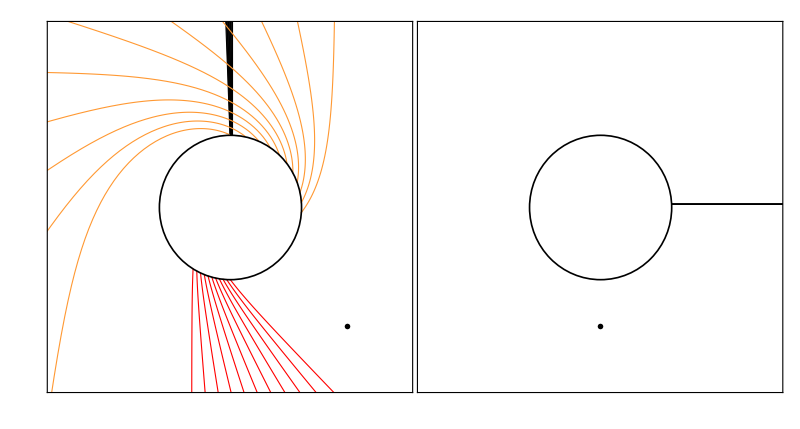

/Users/zhangcong/Desktop/latex_tex/paper/LQBHshadow/shadow2/shadow2_paper2/nullgeos.pdf

```mathematica
plot=Plot[phiout[M,b],{b, 10^-11,bcri[M]-10^-5},PlotRange->All];
data=Cases[plot,_Line,Infinity];
data=List@@@data//Flatten[#,1]&;
fit1=Interpolation[data[[1]]];
fit2=Interpolation[data[[2]]];
xrange=fit1[[1,1]];
b2=Table[bisection[fit2[#]-Pi/2-n Pi&,xrange[[1]],xrange[[2]],10^-8],{n,0,4}];
b1=Table[bisection[fit1[#]-Pi/2-n Pi&,xrange[[1]],xrange[[2]],10^-8],{n,0,4}];
rangeb=MapThread[Range[#1,#2,(#2-#1)/10]&,{b2,b1}];
color={Black,Red,RGBColor[1,0.6,0.2],Blue};
plotrange=1300/263.;
p0=Plot[{},{x,-plotrange,plotrange},PlotStyle->White];
thetickes=maTexTicks[{{-plotrange,plotrange},{-plotrange,plotrange}},{Identity,Identity},{Identity,Identity},1,True,False];
p0=p0/.{Rule[FrameTicks,_]:>Rule[FrameTicks,{{thetickes[[2]],Automatic},{thetickes[[1]],Automatic}}]};
p1=Show[{p0,
Table[plotgeo[b,M,{Thickness[0.002],color[[1]]}],{b,rangeb[[1]]}],
Table[plotgeo[b,M,{Thickness[0.002],color[[2]]}],{b,rangeb[[2]]}],
Table[plotgeo[b,M,{Thickness[0.002],color[[3]]}],{b,rangeb[[3]]}],
Graphics[{
{Thickness[0.003],Circle[{0,0},horizons[M][[2]]]},
Inset[MaTeX["A \\text{ Region}",Magnification->1.2],{0,-plotrange 2/3}]
}
]
},
Frame->True,Axes->False,PlotRange->{{-plotrange,plotrange},{-plotrange,plotrange}},
ImagePadding->{{Automatic,Automatic}, {Automatic,30}},AspectRatio->1
];
p0=Plot[{},{x,-plotrange,plotrange},PlotStyle->White];
thetickes=maTexTicks[{{-plotrange,plotrange},{-plotrange,plotrange}},{Identity,Identity},{Identity,Identity},1,True];
p0=p0/.{Rule[FrameTicks,_]:>Rule[FrameTicks,{{thetickes[[2]],Automatic},{thetickes[[1]],Automatic}}]};
p2=Show[{p0,
Table[plotgeop[b,M,{Thickness[0.002],color[[1]]}],{b,rangeb[[1]]}],
Table[plotgeop[b,M,{Thickness[0.002],color[[2]]}],{b,rangeb[[2]]}],
Table[plotgeop[b,M,{Thickness[0.002],color[[3]]}],{b,rangeb[[3]]}],
Graphics[{{Thickness[0.003],Circle[{0,0},horizons[M][[2]]]},
,
Inset[MaTeX["A' \\text{ Region}",Magnification->1.2],{3.3,-plotrange 2/3}]
}](*,
ParametricPlot[{0,y},{y,horizons[betav][[2]],6},PlotStyle->{DotDashed,Thickness[0.003],Black}],
ParametricPlot[{0,y},{y,-horizons[betav][[2]],-6},PlotStyle->{DotDashed,Thickness[0.003],Black}]*)
},
Frame->True,Axes->False,PlotRange->{{-plotrange,plotrange},{-plotrange,plotrange}},AspectRatio->1
];
p3=GraphicsGrid[{{p2,p1}},Spacings->-50]
Export["/Users/zhangcong/Desktop/latex_tex/paper/LQBHshadow/shadow2/shadow2_paper2/nullgeos.pdf",p3,"PDF"]
```

```mathematica
FrameLabel
```

### Shadow Image

```mathematica
betav=0.98;
M=√((4 (betav^4) )/(1-betav^2)^3 alpha)
Iemo[r_,M_]:=If[r>1/umin[M],(1/(r-(1/umin[M]-1))^3),0]
emissionbs=criPhisofb[M,0,4]
```

263.239

{{0.0715482,1.07743,2.97386,4.41407,4.99477},{0.0758542,1.51209,4.37333,5.14566,5.19416},4.45728}

```mathematica
Do[phioutexpl[m]=bisection[phioutLargeM[#,M]-(2m-1)Pi/2&,0.01,5.196,10^-8]//Chop,{m,1,4}]
```

```mathematica
Do[phitotexpl[m]=bisection[phitotLargeM[#,M]-(2m-1)Pi/2&,0.01,5.196,10^-8]//Chop,{m,1,4}]
```

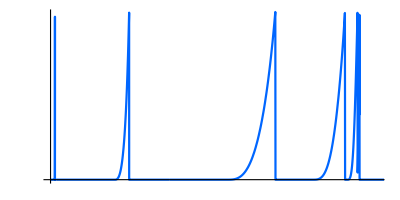

```mathematica
xrange=8.5;
p0e=Plot[-0.1,{x,0,xrange},PlotRange->{{0,xrange},{0.,1}},PlotStyle->Directive[Opacity[0]],AxesLabel->{MaTeX["r/M",Magnification->1.4],MaTeX["I_{\\rm em}/I_0",Magnification->1.4]}];
thetickes=maTexTicks[{{0,xrange},{0.,1}},{Identity,Identity},{Identity,Identity},3,True,True,1.4]/.AbsoluteThickness[x_]:>AbsoluteThickness[5x];
p0e=p0e/.{Rule[Ticks,_]:>Rule[Ticks,thetickes]};
pe=Plot[Iemo[r ,M],{r,0,xrange},PlotRange->All,PlotStyle->Black,AspectRatio->1/2];
se=Show[{p0e,pe},AspectRatio->1/2,ImageSize->{400,200}];
p1=Plot[Iob[Iemo[#,M]&,_,b ,M,"Wh"],{b,0,0.1},PlotRange->All,PlotStyle->RGBColor[0,0.4,1]];
p1p=Plot[Iob[Iemo[#,M]&,_,b,M,"Wh"],{b,0.1,2},PlotRange->All,PlotStyle->RGBColor[0,0.4,1]];
p1pp=Plot[Iob[Iemo[#,M]&,_, b,M,"Wh"],{b,2,12},PlotRange->All,PlotStyle->RGBColor[0,0.4,1]];
xrange=5.5;
p0=Plot[-0.1,{x,0,xrange},PlotStyle->Directive[Opacity[0]],AxesLabel->{MaTeX["b/M",Magnification->1.4],MaTeX["I^{\\rm obs}/I_0",Magnification->1.4]},PlotRange->{{0,xrange},{0.,0.11}}];
thetickes=maTexTicks[{{0,xrange},{0.,0.11}},{Identity,Identity},{Identity,Identity},3,True,True,1.4]/.AbsoluteThickness[x_]:>AbsoluteThickness[5x];
p0=p0/.{Rule[Ticks,_]:>Rule[Ticks,thetickes]};
so1=Show[{p0,p1,p1p,p1pp},ImageSize->{400,200},AspectRatio->1/2]
```

```mathematica
Iobb=List@@(Cases[p1,_Line,Infinity]//First)//First//Chop;
Iobb=Join[Iobb,List@@(Cases[p1p,_Line,Infinity]//First)//First//Chop];
Iobb=Join[Iobb,List@@(Cases[p1pp,_Line,Infinity]//First)//First//Chop];
Iobbp=Tuples[{Iobb,Range[0,2Pi,Pi/50]}];
Iobbp=ParallelMap[{#[[1,1]]Cos[#[[2]]],#[[1,1]]Sin[#[[2]]],#[[1,2]]}&,Iobbp];
plotrange=0.08;
s20=ListDensityPlot[Iobbp,ColorFunction->(ColorData[{"SunsetColors",{0,0.15}}]),ColorFunctionScaling->False,PlotLegends->None,ImageSize->{180,180},Frame->False,PlotRange->{{-plotrange,plotrange},{-plotrange,plotrange}}];
plotrange=5.5;
s21=ListDensityPlot[Iobbp,ColorFunction->(ColorData[{"SunsetColors",{0,0.15}}]),ColorFunctionScaling->False,PlotLegends->None,ImageSize->{250,250},Frame->False,PlotRange->{{-plotrange,plotrange},{-plotrange,plotrange}}];
```

```mathematica
s1=GraphicsGrid[{{se},{so1}},Spacings->-0];
s2p=GraphicsGrid[{{s20},{s21}},Spacings->-10,ImageSize->{200,350}];
s2p=Show[{s2p,Graphics[{
{Directive[White,Dashed,Thick],Line[{{117.3,-358.5},{43,-234}}]},
{Directive[Black,Dashed,Thick],Line[{{43,-234},{28,-210}}]},
{Directive[White,Dashed,Thick],Line[{{121.3,-358.5},{197,-233}}]},
{Directive[Black,Dashed,Thick],Line[{{197,-233},{210,-210}}]}
}]}];
```

```mathematica
s3=GraphicsGrid[{{s1,s2p}},Spacings->-80,ImageSize->{1000,700},Alignment->Center]
(*Export["/Users/zhangcong/Desktop/latex_tex/paper/LQBHshadow/shadow2/shadow2_paper/shadow.eps",s3,"EPS",ImageSize->{1000,700},ImageResolution->800]*)
```

-Graphics-

```mathematica
pbh=Plot[Iob[_,Iemo[#,M]&,b,M,"Bh"],{b,0,12},PlotRange->All,PlotStyle->{Red,Dashed}];
Iobbh=List@@(Cases[pbh,_Line,Infinity]//First)//First//Chop;
Iobbhp=Tuples[{Iobbh,Range[0,2Pi,Pi/50]}];
Iobbhp=ParallelMap[{#[[1,1]]Cos[#[[2]]],#[[1,1]]Sin[#[[2]]],#[[1,2]]}&,Iobbhp];
plotrange=5.5;
sbh=ListDensityPlot[Iobbhp,ColorFunction->(ColorData[{"SunsetColors",{0,0.15}}]),ColorFunctionScaling->False,PlotLegends->None,ImageSize->{200,200},Frame->False,PlotRange->{{-plotrange,plotrange},{-plotrange,plotrange}}];
```

```mathematica
p1bwh=Plot[Iob[Iemo[#,M]&,Iemo[#,M]&,b ,M,"Bh-Wh"],{b,0,0.1},PlotRange->All,PlotStyle->RGBColor[0,0.4,1]];
p1bwhp=Plot[Iob[Iemo[#,M]&,Iemo[#,M]&,b ,M,"Bh-Wh"],{b,0.1,2},PlotRange->All,PlotStyle->RGBColor[0,0.4,1]];
p1bwhpp=Plot[Iob[Iemo[#,M]&,Iemo[#,M]&,b ,M,"Bh-Wh"],{b,2,12},PlotRange->All,PlotStyle->RGBColor[0,0.4,1]];
```

```mathematica
Iobbwh=List@@(Cases[p1bwh,_Line,Infinity]//First)//First//Chop;
Iobbwh=Join[Iobbwh,List@@(Cases[p1bwhp,_Line,Infinity]//First)//First//Chop];
Iobbwh=Join[Iobbwh,List@@(Cases[p1bwhpp,_Line,Infinity]//First)//First//Chop];
```

```mathematica
Iobbwhp=Tuples[{Iobbwh,Range[0,2Pi,Pi/50]}];
Iobbwhp=ParallelMap[{#[[1,1]]Cos[#[[2]]],#[[1,1]]Sin[#[[2]]],#[[1,2]]}&,Iobbwhp];
plotrange=0.08;
swbh0=ListDensityPlot[Iobbwhp,ColorFunction->(ColorData[{"SunsetColors",{0,0.15}}]),ColorFunctionScaling->False,PlotLegends->None,ImageSize->{120,120},Frame->False,PlotRange->{{-plotrange,plotrange},{-plotrange,plotrange}}];
plotrange=5.5;
swbh=ListDensityPlot[Iobbwhp,ColorFunction->(ColorData[{"SunsetColors",{0,0.15}}]),ColorFunctionScaling->False,PlotLegends->None,ImageSize->{250,250},Frame->False,PlotRange->{{-plotrange,plotrange},{-plotrange,plotrange}}];
```

```mathematica
swbh2=GraphicsGrid[{{swbh0},{swbh}},Spacings->-45,ImageSize->{200,350}];
swbh2=Show[{swbh2,Graphics[{
{Directive[White,Dashed,Thick],Line[{{100.,-306.2},{47.5,-181.}}]},
{Directive[Black,Dashed,Thick],Line[{{47.5,-181.},{40.87,-163.7}}]},
{Directive[White,Dashed,Thick],Line[{{104,-306.2},{155,-181}}]},
{Directive[Black,Dashed,Thick],Line[{{155,-181},{161.9,-163.7}}]}
}]}];
```

```mathematica
plotrange=0.08;
s20=ListDensityPlot[Iobbp,ColorFunction->(ColorData[{"SunsetColors",{0,0.15}}]),ColorFunctionScaling->False,PlotLegends->None,ImageSize->{120,120},Frame->False,PlotRange->{{-plotrange,plotrange},{-plotrange,plotrange}}];
plotrange=5.5;
s21=ListDensityPlot[Iobbp,ColorFunction->(ColorData[{"SunsetColors",{0,0.15}}]),ColorFunctionScaling->False,PlotLegends->None,ImageSize->{250,250},Frame->False,PlotRange->{{-plotrange,plotrange},{-plotrange,plotrange}}];
```

```mathematica
se=Show[p0e,pe,AspectRatio->0.5,ImageSize->{400,200}];
so1=Show[{p0,p1,p1p,p1pp},ImageSize->{400,200},AspectRatio->0.5];
s1=GraphicsGrid[{{se},{so1}},Spacings->-0];
s2p=GraphicsGrid[{{s20},{s21}},Spacings->-45,ImageSize->{400,220}];
s2p=Show[{s2p,Graphics[{
{Directive[White,Dashed,Thick],Line[{{100.,-306.2},{47.5,-181.}}]},
{Directive[Black,Dashed,Thick],Line[{{47.5,-181.},{40.87,-163.7}}]},
{Directive[White,Dashed,Thick],Line[{{104,-306.2},{155,-181}}]},
{Directive[Black,Dashed,Thick],Line[{{155,-181},{161.9,-163.7}}]}
}]}];
```

```mathematica
s3p=GraphicsGrid[{{s1,s2p}},Spacings->-140,ImageSize->{900,500},Alignment->Center];
sbbwh=GraphicsGrid[{{sbh},{swbh2}},Spacings->-80,ImageSize->{250,500},Alignment->Center];
```

```mathematica
stot=GraphicsGrid[{{s3p,sbbwh}},Spacings->-490,ImageSize->{800,400},Alignment->Center]
(*Export["/Users/zhangcong/Desktop/latex_tex/paper/LQBHshadow/shadow2/shadow2_paper2/shadowtot.eps",stot,"EPS",ImageSize->{800,400},ImageResolution->800]*)
```

-Graphics-

## The Penrose diagram

```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{bm}","\\usepackage{mathrsfs}"}];
labels=Graphics[{
{Blue,Disk[{0.91,2.8},0.03]},
{RGBColor[1,0.6,0.2],Disk[{0.94,-0.47},0.03]},
Inset[MaTeX["i^-",Magnification->1.5],{-1.15Pi/4,-1.1Pi/4}],
Inset[MaTeX["i^-",Magnification->1.5],{1.15Pi/4,-1.1Pi/4}],
Inset[MaTeX["i^+",Magnification->1.5],{-1.15Pi/4,1.0Pi/4}],
Inset[MaTeX["i^+",Magnification->1.5],{1.15Pi/4,1.04Pi/4}],
Inset[MaTeX["i^-",Magnification->1.5],{-1.15Pi/4,-1.1Pi/4+Pi}],
Inset[MaTeX["i^-",Magnification->1.5],{1.15Pi/4,-1.1Pi/4+Pi}],
Inset[MaTeX["i^+",Magnification->1.5],{-1.15Pi/4,1.0Pi/4+Pi}],
Inset[MaTeX["i^+",Magnification->1.5],{1.15Pi/4,1.04Pi/4+Pi}],
Inset[MaTeX["i^0",Magnification->1.5],{-1.05Pi/2,0}],
Inset[MaTeX["i^0",Magnification->1.5],{1.06Pi/2,0}],
Inset[MaTeX["i^0",Magnification->1.5],{-1.05Pi/2,Pi}],
Inset[MaTeX["i^0",Magnification->1.5],{1.06Pi/2,Pi}],
Inset[MaTeX["r_+",Magnification->1.5],{1.4Pi/8,1Pi/8}],
Inset[MaTeX["r_+",Magnification->1.5],{-1.3Pi/8,1.1Pi/8}],
Inset[MaTeX["r_+",Magnification->1.5],{1.4Pi/8,-1Pi/8}],
Inset[MaTeX["r_+",Magnification->1.5],{-1.3Pi/8,-0.32}],
Inset[MaTeX["r_+",Magnification->1.5],{1.4Pi/8,1Pi/8+Pi}],
Inset[MaTeX["r_+",Magnification->1.5],{-1.3Pi/8,1.1Pi/8+Pi}],
Inset[MaTeX["r_+",Magnification->1.5],{-1.3Pi/8,2.82}],
Inset[MaTeX["r_+",Magnification->1.5],{0.45,2.6}],
Inset[MaTeX["r_-",Magnification->1.5],{1.4Pi/8,1Pi/8+Pi/2}],
Inset[MaTeX["r_-",Magnification->1.5],{-1.3Pi/8,2.23}],
Inset[MaTeX["r_-",Magnification->1.5],{1.4Pi/8,-1Pi/8+Pi/2}],
Inset[MaTeX["r_-",Magnification->1.5],{-0.52,0.9}],
Inset[MaTeX["r_-",Magnification->1.5],{1.4Pi/8,1Pi/8-Pi/2}],
Inset[MaTeX["r_-",Magnification->1.5],{-1.3Pi/8,1.1Pi/8-Pi/2}],
Inset[MaTeX["r_-",Magnification->1.5],{1.4Pi/8,-1Pi/8+3Pi/2}],
Inset[MaTeX["r_-",Magnification->1.5],{-1.3Pi/8,-0.9Pi/8+3Pi/2}],
Inset[MaTeX["\\mathscr{I}_-",Magnification->1.5],{1.65Pi/4,-1.1Pi/8}],
Inset[MaTeX["\\mathscr{I}_-",Magnification->1.5],{-1.65Pi/4,-1.1Pi/8}],
Inset[MaTeX["\\mathscr{I}_+",Magnification->1.5],{1.65Pi/4,3.65}],
Inset[MaTeX["\\mathscr{I}_+",Magnification->1.5],{-1.65Pi/4,3.65}],
Inset[MaTeX["\\mathscr{I}_+",Magnification->1.5],{1.65Pi/4,1.1Pi/8}],
Inset[MaTeX["\\mathscr{I}_+",Magnification->1.5],{-1.65Pi/4,0.5}],
Inset[MaTeX["\\mathscr{I}_-",Magnification->1.5],{1.65Pi/4,-1.1Pi/8+4Pi/4}],
Inset[MaTeX["\\mathscr{I}_-",Magnification->1.5],{-1.65Pi/4,-1.1Pi/8+4Pi/4}],
Inset[MaTeX["A'",Magnification->2],{1.4Pi/4,0}],
Inset[MaTeX["D'",Magnification->2],{-1.2Pi/4,0}],
Inset[MaTeX["A",Magnification->2],{0.68,3.}],
Inset[MaTeX["D",Magnification->2],{-1.2Pi/4,Pi}],
Inset[MaTeX["B'",Magnification->2],{0,1.2Pi/4}],
Inset[MaTeX["W'",Magnification->2],{0,-0.8Pi/4}],
Inset[MaTeX["W",Magnification->2],{0,3.2Pi/4}],
Inset[MaTeX["B",Magnification->2],{0,5Pi/4}],
Inset[MaTeX["C'",Magnification->2],{0.5,Pi/2}],
Inset[MaTeX["C",Magnification->2],{-0.5,Pi/2}],
Inset[MaTeX[" ",Magnification->2],{-1.8,Pi/2}],
Inset[MaTeX[" ",Magnification->1],{1.8,Pi/2}]
}];
```

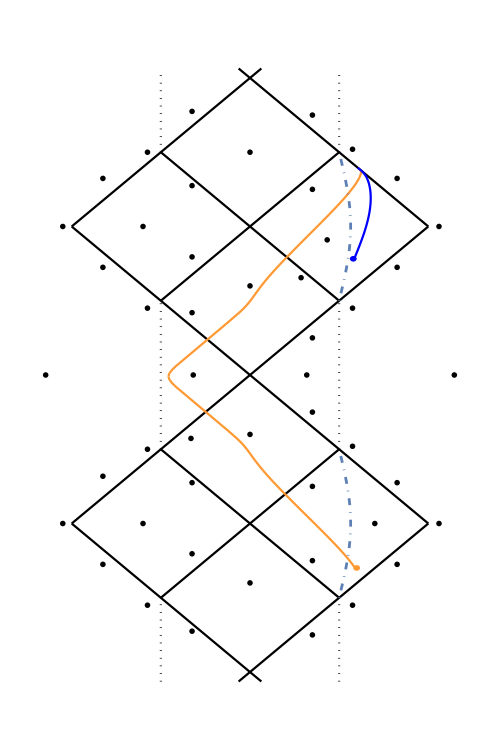

/Users/zhangcong/Desktop/latex_tex/paper/LQBHshadow/shadow2/shadow2_paper2/penrose.pdf

```mathematica
boundaries={
Plot[Pi/2-X,{X,-Pi/2,2Pi/4},PlotRange->All,PlotStyle->Black],
Plot[Pi-X,{X,-Pi/4,Pi/4},PlotRange->All,PlotStyle->Black],
Plot[Pi/2+X,{X,-Pi/2,2Pi/4},PlotRange->All,PlotStyle->Black],
Plot[Pi+X,{X,-Pi/4,Pi/4},PlotRange->All,PlotStyle->Black],
Plot[3Pi/2+X,{X,-Pi/2,0.1},PlotRange->All,PlotStyle->Black],
Plot[3Pi/2-X,{X,-0.1,Pi/2},PlotRange->All,PlotStyle->Black],
Plot[-Pi/2+X,{X,-0.1,Pi/2},PlotRange->All,PlotStyle->Black],
Plot[-Pi/2-X,{X,-Pi/2,0.1},PlotRange->All,PlotStyle->Black],
Plot[-X,{X,-Pi/4,Pi/4},PlotRange->All,PlotStyle->Black],
Plot[X,{X,-Pi/4,Pi/4},PlotRange->All,PlotStyle->Black],
ParametricPlot[{-Pi/4,x},{x,-Pi/2-0.1,-Pi/4},PlotStyle->{Dotted,Black}],
ParametricPlot[{Pi/4,x},{x,-Pi/2-0.1,-Pi/4},PlotStyle->{Dotted,Black}],
ParametricPlot[{-Pi/4,x},{x,Pi/4,3Pi/4},PlotStyle->{Dotted,Black}],
ParametricPlot[{Pi/4,x},{x,Pi/4,3Pi/4},PlotStyle->{Dotted,Black}],
ParametricPlot[{-Pi/4,x},{x,5Pi/4,6Pi/4+0.1},PlotStyle->{Dotted,Black}],
ParametricPlot[{Pi/4,x},{x,5Pi/4,6Pi/4+0.1},PlotStyle->{Dotted,Black}]
};
betav=0.55;
bv=bcri[betav]-2;
{{geowv,{iniv,tv}},{geowu,{iniu,tu}},vp,up,betav}=geoInPenrose[bv,betav,-6];
bvp=bcri[betav]+0.001;
{{geowvp,{inivp,tvp}},{geowup,{iniup,tup}},vpp,upp,betav}=geoInPenrose[bvp,betav,-47];

M=√((4 (betav^4) )/(1-betav^2)^3 alpha);ap=(M (1+betav)^2 (-1+Sqrt[-1+2 betav]+betav (3+betav+2 Sqrt[-1+2betav])))/(4 betav Sqrt[-1+2 betav] (2+betav^2));
am=(M (1+betav)^2 (-1-Sqrt[-1+2 betav]+betav (3+betav-2 Sqrt[-1+2 betav])))/(4 betav Sqrt[-1+2 betav] (2+betav^2));

pgeodesic2=Show[{boundaries,labels,
ParametricPlot[coorv[1/geowv[v],ArcTan[Exp[1/(2ap) v]],betav],{v,iniv+2,vp},PlotStyle->{RGBColor[1,0.6,0.2]},PlotRange->All],
ParametricPlot[coortildv[1/geowv[v],ArcTan[Exp[1/(2ap) v]],betav],{v,vp,tv},PlotStyle->{RGBColor[1,0.6,0.2]}],
ParametricPlot[coortildu[1/geowu[u],Pi-ArcTan[Exp[-1/(2ap)u]],betav],{u,iniu,up},PlotStyle->{RGBColor[1,0.6,0.2]}],
ParametricPlot[coorbaru[1/geowu[u],Pi+ArcTan[-Exp[-1/(2ap)u]],betav],{u,up,tu},PlotStyle->{RGBColor[1,0.6,0.2]}],
ParametricPlot[coorbaru[1/geowup[u],Pi+ArcTan[-Exp[-1/(2ap)u]],betav],{u,tup-12,tup},PlotStyle->{Blue}],
ParametricPlot[coorbaru[1/umin[betav],Pi+ArcTan[-Exp[-1/(2ap)u]],betav],{u,-100,100},PlotStyle->{DotDashed,Thickness[0.004]}],
ParametricPlot[cooru[1/umin[betav],ArcTan[-Exp[-1/(2ap)u]],betav],{u,-100,100},PlotStyle->{DotDashed,Thickness[0.004]}]
},FrameTicks->None,Axes->False,AspectRatio->1.5,ImageSize->{500,500}]
Export["/Users/zhangcong/Desktop/latex_tex/paper/LQBHshadow/shadow2/shadow2_paper2/penrose.pdf",pgeodesic2,"PDF"]
```

```mathematica
1/1.5
```

0.666667

## Get b_π for Δϕ=π

```mathematica
eq1=CoefficientList[A1 (x-a)^2+B1(x-b)^2,x]=={-x1,1,0}//Thread;
eq2=CoefficientList[A2 (x-a)^2+B2(x-b)^2,x]==CoefficientList[2(x-x2-I x3)(x-x2+I x3),x]//Thread;
eqs=Join[eq1,eq2];
sol=Solve[eqs,{A1,B1,A2,B2,a,b}]//FullSimplify//First
roots=y/.Solve[2 y^3-y^2+β^-2==0,y];
ruleAbab={x2->1/2(roots[[1]]+roots[[3]]),x3->1/(2I)(roots[[1]]-roots[[3]]),x1->roots[[2]]}//FullSimplify;
ruleAbab=ruleAbab/.{ 1+(6 (-9+√(81-3 β^2)))/β^2->-AA,2+(12 (-9+√(81-3 β^2)))/β^2->-2 AA}//FullSimplify[#,AA>0]&//FullSimplify
```

{A1→-1/(4 √((x1-x2)^2+x3^2)),B1→1/(4 √((x1-x2)^2+x3^2)),A2→(-x1+x2+√((x1-x2)^2+x3^2))/(√((x1-x2)^2+x3^2)),B2→(x1-x2+√((x1-x2)^2+x3^2))/(√((x1-x2)^2+x3^2)),a→x1+√((x1-x2)^2+x3^2),b→x1-√((x1-x2)^2+x3^2)}

{x2→((1+AA^(1/3))^2)/(12 AA^(1/3)),x3→(-1+AA^(2/3))/(4 √3 AA^(1/3)),x1→1/6 (1-(1+AA^(2/3))/AA^(1/3))}

```mathematica
kk=A2/(A2+B2)/.sol//FullSimplify;
kk=kk/.ruleAbab//FullSimplify[#,AA>0]&;
kk=kk/. 1/(√(1+1/AA^(2/3)+AA^(2/3)) AA^(1/3))->1/√(1+AA^(2/3)+AA^(4/3))
coe=(a-b)^-1/(√(B1(A2+B2)))/.sol//FullSimplify
coe=coe/.ruleAbab//FullSimplify[#,AA>0]&
coe √(a-b)/.sol//FullSimplify
%/.ruleAbab//FullSimplify[#,AA>0]&
```

```mathematica
(1/2-a)/(1/2-b)/.sol//FullSimplify
%/.ruleAbab//FullSimplify[#,AA>0]&
%/.√(1+1/AA^(2/3)+AA^(2/3))->√(AA^(2/3)+1+AA^(4/3))AA^(-1/3)//FullSimplify
```

-(-1/2+x1+√((x1-x2)^2+x3^2))/(1/2-x1+√((x1-x2)^2+x3^2))

(1+(2-√3 √(1+1/AA^(2/3)+AA^(2/3))) AA^(1/3)+AA^(2/3))/(1+(2+√3 √(1+1/AA^(2/3)+AA^(2/3))) AA^(1/3)+AA^(2/3))

(1+2 AA^(1/3)+AA^(2/3)-√3 √(1+AA^(2/3)+AA^(4/3)))/(1+2 AA^(1/3)+AA^(2/3)+√3 √(1+AA^(2/3)+AA^(4/3)))

## Compare null geo and free falling geo

```mathematica
M=250.;
```

```mathematica
F[w_,M_]:=w^2(alpha M^2 w^4-2 M w+1)
Fw2[w_,M_]:=alpha M^2 w^4-2 M w+1
Gn[w_,bv_,M_]:=(1+Re@√(1-bv^2 F[w,M]))Re@√(1-bv^2 F[w,M])/bv^2
Gt[w_,M_]:=w^2(1+Re@√(1-Fw2[w,M]))Re@√(1-Fw2[w,M])
Gtp[w_,M_]:=-w^2(1-Re@√(1-Fw2[w,M]))Re@√(1-Fw2[w,M])
rstar[r_,M_]:=Block[{beta,x,rp,rm,am,ap,b1,b0,re,re1,W0,Wr},
beta=x/.NSolve[{M^2==(4 x^4)/((1-x^2)^3)alpha,x>0,x<1},x]//First;
{rm,rp}=horizons[beta];
b0=( M^2 (-2+beta) (-1+beta)^3 (1+beta))/(4 beta^2 (2+beta^2));
ap=(M (1+beta)^2 (-1+Sqrt[-1+2 beta]+beta (3+beta+2 Sqrt[-1+2beta])))/(4 beta Sqrt[-1+2 beta] (2+beta^2));
b1=(M (-1+beta)^2 (-1+2 beta))/(2 beta (2+beta^2));
am=(M (1+beta)^2 (-1-Sqrt[-1+2 beta]+beta (3+beta-2 Sqrt[-1+2 beta])))/(4 beta Sqrt[-1+2 beta] (2+beta^2));
W0=((1-beta)^2 (beta+1))/(2beta^2) M^2;
Wr=r^2+(1/beta-1) M r+((1-beta)^2 (beta+1))/(2beta^2) M^2;
re=r+ap Log[Abs[r-rp]/rp]-am Log[Abs[r-rm]/rm]+1/2 b1 Log[Wr/W0];
re1=-(2beta b0/M+b1(1-beta))/((1-beta)√(1+2beta))(ArcTan[(1-beta+2beta r/M)/((1-beta)√(1+2 beta))]-ArcTan[1/(√(1+2 beta))]);
re=re+re1
]
geoDustSurface[M_,vplowerLim_,vpupperLim_,vmlowerLim_,vmupperLim_,alpha_:(6859 √3 π)/32000]:=Block[{beta,x,rp,rm,wb,inivp,solt1,solt1p,wtp,geotvp,ep,vmtb,inivm,solt2,solt2p,wtm,geotvm},
beta=x/.NSolve[{M^2==(4 x^4)/((1-x^2)^3)alpha,x>0,x<1},x]//First;
{rm,rp}=horizons[beta];
wb=((alpha M)/2)^(-1/3);
inivp=-NIntegrate[1/Gt[x,M],{x,0.99wb,wb}];
solt1=NDSolve[{D[wtp[vp],vp]==Gt[wtp[vp],M],wtp[inivp]==0.99wb},wtp,{vp,vplowerLim,0}];
ep=10^-10;
inivp=(3 2^(2/3) (M alpha)^(2/3) ep+4 2^(1/3) √3 M √(alpha ep^3)+2 √3 M^(1/3) alpha^(5/6) √ep (1+ep))/(6 (M alpha)^(1/3));
solt1p=NDSolve[{D[wtp[vp],vp]==Gtp[wtp[vp],M],wtp[inivp]==(1-ep)wb},wtp,{vp,0,vpupperLim}];

vmtb=-2rstar[1/wb,M];
inivm=NIntegrate[1/(-Gt[x,M]),{x,0.99wb,wb}];
inivm=vmtb-inivm;
solt2=NDSolve[{D[wtm[vm],vm]==-Gt[wtm[vm],M],wtm[inivm]==0.99wb},wtm,{vm,vmtb,vmupperLim}];
solt2p=NDSolve[{D[wtm[vm],vm]==-Gtp[wtm[vm],M],wtm[vmtb-inivp]==(1-ep)wb},wtm,{vm,vmlowerLim,vmtb}];
geotvp=wtp/.{solt1[[1]],solt1p[[1]]};
geotvm=wtm/.{solt2p[[1]],solt2[[1]]};
{{geotvp,{{vplowerLim,0},{0,vpupperLim}}}//Transpose,{geotvm,{{vmlowerLim,vmtb},{vmtb,vmupperLim}}}//Transpose,{rm,rp}}
]
```

```mathematica
(*Series[1/(-w^2(1-√(-α m^2 w^4+2 m w))√(-α m^2 w^4+2 m w)),{w,((α m)/2)^(-1/3),0}]//FullSimplify[#,w-2^(1/3)/(m α)^(1/3)<0]&//Normal
Integrate[%,w]/.{{w->(1-ϵ)2^(1/3)/(m α)^(1/3)},{w->2^(1/3)/(m α)^(1/3)}}
%[[1]]-%[[2]]//FullSimplify[#,ϵ>0&&m>0&&α>0]&*)
(*epsilon=$MachineEpsilon;
sol1=NDSolve[{D[vm[w],w]==-1/Gn[w,bv,M],vm[0]==vom},vm,{w,0,uroot-epsilon}];
geovm=vm/.sol1[[1]];
vpb=geovm[uroot-epsilon]+2rstar[1/uroot,M];
geovm[uroot-epsilon]
sol2=NDSolve[{D[vp[w],w]==1/Gn[w,bv,M],vp[uroot-epsilon]==vpb},vp,{w,0,uroot-epsilon}];
geovp=vp/.sol2[[1]];
Plot[geovm[x],{x,0,uroot-epsilon},PlotRange->All]*)
```

```mathematica
nullgeouv[bv_,M_]:=Block[{uroot,w,dvmp,vmb,vom,sol1,wm,vpb,vop,sol2,wp,geovm,geovp},
uroot=w/.NSolve[1/bv^2-F[w,M]==0,w];
uroot=Cases[uroot,_?(Element[#,Reals]&&#>0&)]//First;
dvmp=NIntegrate[1/Gn[w,bv,M],{w,0,uroot}];
vpb=0;
vop=vpb-dvmp;
sol1=NDSolve[{D[wp[vp],vp]==Gn[wp[vp],bv,M],wp[vop]==0},wp,{vp,vop,vpb}];
vmb=vpb-2rstar[1/uroot,M];
vom=vmb+dvmp;
sol2=NDSolve[{D[wm[vm],vm]==-Gn[wm[vm],bv,M],wm[vom]==0},wm,{vm,vmb,vom}];
geovp=wp/.sol1[[1]];
geovm=wm/.sol2[[1]];
{{geovp,{vop,vpb}},{geovm,{vmb,vom}},uroot}
]
```

```mathematica
{{geovp,{vop,vpb}},{geovm,{vmb,vom}},uroot}=nullgeouv[0.5M,M]
{{{geotvp,rvp},rest},{rest1,{geotvm,rvm}},{rm,rp}}=geoDustSurface[M,vop,vpb+4,vmb,vom];
```

{{InterpolatingFunction[…],{-61.525,0}},{InterpolatingFunction[…],{-0.381192,61.1438}},0.189331}

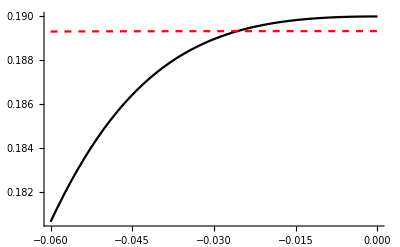

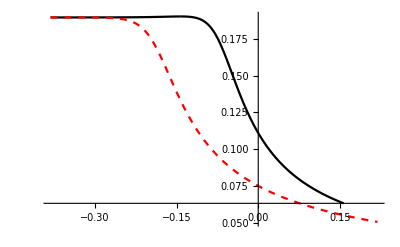

```mathematica
Plot[{geotvp[x],geovp[x]},{x,vpb-0.06,vpb},PlotStyle->{Black,{Red,Dashed}},PlotRange->All]
Show[{Plot[{geotvm[x]},{x,rvm[[1]],rvm[[1]]+0.3},PlotStyle->{Black}],
Plot[rest1[[1]][x],{x,rest1[[2,1]],rest1[[2,2]]},PlotStyle->{Black}],
Plot[geovm[x],{x,vmb,vmb+0.6},PlotStyle->{{Red,Dashed}}]
},PlotRange->All
]
```

```mathematica
(*beta=x/.NSolve[{M^2==(4 x^4)/((1-x^2)^3)alpha,x>0,x<1},x]//First;
{rm,rp}=horizons[beta];
b0=( M^2 (-2+beta) (-1+beta)^3 (1+beta))/(4 beta^2 (2+beta^2));
ap=(M (1+beta)^2 (-1+Sqrt[-1+2 beta]+beta (3+beta+2 Sqrt[-1+2beta])))/(4 beta Sqrt[-1+2 beta] (2+beta^2));
b1=(M (-1+beta)^2 (-1+2 beta))/(2 beta (2+beta^2));
am=(M (1+beta)^2 (-1-Sqrt[-1+2 beta]+beta (3+beta-2 Sqrt[-1+2 beta])))/(4 beta Sqrt[-1+2 beta] (2+beta^2));
W0=((1-beta)^2 (beta+1))/(2beta^2) M^2;
Wr=r^2+(1/beta-1) M r+((1-beta)^2 (beta+1))/(2beta^2) M^2;
Off[General::munfl,Power::infy]
Show[{
ParametricPlot[coorv[1/geovp[v],ArcTan[Exp[1/(2ap) v]],beta],{v,vop+2,vpb},PlotStyle->{Red},PlotRange->All],
ParametricPlot[coortildv[1/geovp[v],ArcTan[Exp[1/(2ap) v]],beta],{v,vop,vpb},PlotStyle->{Red}],
ParametricPlot[coortildu[1/geovm[u],Pi-ArcTan[Exp[-1/(2ap)u]],beta],{u,vmb,vom},PlotStyle->{Red}],
ParametricPlot[coorbaru[1/geovm[u],Pi+ArcTan[-Exp[-1/(2ap)u]],beta],{u,vmb,vom},PlotStyle->{Red}],
ParametricPlot[coorv[1/geotvp[v],ArcTan[Exp[1/(2ap) v]],beta],{v,-1000,0},PlotStyle->{Dashed,Black},PlotRange->All],
ParametricPlot[coortildv[1/geotvp[v],ArcTan[Exp[1/(2ap) v]],beta],{v,-1000,0},PlotStyle->{Dashed,Black}],
ParametricPlot[coortildu[1/geotvm[u],Pi-ArcTan[Exp[-1/(2ap)u]],beta],{u,vmtb,vmtb+1000},PlotStyle->{Dashed,Black}],
ParametricPlot[coorbaru[1/geotvm[u],Pi+ArcTan[-Exp[-1/(2ap)u]],beta],{u,vmtb,vmtb+1000},PlotStyle->{Dashed,Black}]
}]*)
```

## Condition s.t. LQGBH taking Schwarzschild as limit

```mathematica
β=1;
λ=-(6(√(81-3 β^2)-9))/β^2-1.;
kk=1/4((√3(λ^(2/3)+1))/(√(λ^(2/3)+λ^(4/3)+1))+2);
coe=(3^(1/4)λ^(1/6))/((λ^(2/3)+λ^(4/3)+1)^(1/4));
{x1,x2,x3}={#[[1]],1/2(#[[2]]+#[[3]]),1/(2 I)(#[[2]]-#[[3]])}&@(y/.Solve[2 y^3-y^2+β^-2==0,y])//FullSimplify;
a=√((x1-x2)^2+x3^2)+x1//N;
b=-√((x1-x2)^2+x3^2)+x1//N;
Mv=10000000.;
uroot=Cases[r/.Solve[-Mv^2 r^8+Mv^2 r^6+2 Mv r^3-r^2+Mv^-2==0,r],_?(Element[#,Reals]&&#>0&)]//First
NIntegrate[1/(√(-Mv^2 r^8+Mv^2 r^6+2 Mv r^3-r^2+Mv^-2)),{r,0,uroot}]
coe EllipticF[ArcCos[a/b],kk]-(x √(4+2 Mv x^3) Hypergeometric2F1[-1/6,1/2,5/6,-(Mv x^3)/2])/(√(Mv x^3 (2+Mv x^3)))/.x->uroot

+NIntegrate[1/(√(-Mv^2 x^8+Mv^2 x^6+2 Mv x^3))-1/(√(Mv^2 x^6+2 Mv x^3)),{x,10^-10,uroot}]
-2^(1/3)√Pi Gamma[5/6]/Gamma[1/3] Mv^(-1/3)
```

1.

2.42688

2.42688

3.06508×10^-7

-0.00436751

```mathematica
-2^(1/3)√Pi Gamma[5/6]/Gamma[1/3] Mv^(-1/3)
```

```mathematica
Integrate[1/(√(2 M r^3)),r]
```

-(√2 r)/(√(M r^3))

```mathematica
Integrate[Series[1/(√(F[x] x^3)),{x,0,2}]//FullSimplify[#,x>0]&,x]/. F[0]->2 M
Series[1/(√(-M^2 x^8+M^2 x^6+2 M x^3))-1/(√(M^2 x^6+2 M x^3)),{M,Infinity,1}]//FullSimplify[#,M>0&&x>0]&
Integrate[Series[1/(√(-M^2 x^8+M^2 x^6+2 M x^3))-1/(√(M^2 x^6+2 M x^3)),{M,Infinity,1}]//FullSimplify[#,M>0&&x>0]&,x]
Limit[%,x->1]
Integrate[1/(√(M^2 x^6+2 M x^3)),x]
```

-(√2)/(√M √x)-(F'[0] √x)/(2 (√2 M^(3/2)))+((3 F'[0]^2-4 M F''[0]) x^(3/2))/(48 √2 M^(5/2))+((-15 F'[0]^3+36 M F'[0] F''[0]-16 M^2 F^(3)[0]) x^(5/2))/(960 √2 M^(7/2))+O[x]^(7/2)

(-1+1/(√(1-x^2)))/(x^3 M)+O[1/M]^2

((-1+x^2+√(1-x^2))/(x^2 √(1-x^2))-ArcTanh[√(1-x^2)])/(2 M)+O[1/M]^2

1/(2 M)

-(x √(4+2 M x^3) Hypergeometric2F1[-1/6,1/2,5/6,-(M x^3)/2])/(√(M x^3 (2+M x^3)))

```mathematica
Series[r/.Solve[-M^2 r^6+2 M r^3-r^2+M^-2==0,r],{M,Infinity,1}]//N
Series[r/.Solve[-M^2 r^8+M^2 r^6+2 M r^3-r^2+M^-2==0,r],{M,Infinity,1}]//N
```

{-0.657298/M+O[1/M]^2,1.25992 (1/M)^(1/3)-0.166667/M+O[1/M]^(4/3),-(0.629961+1.09112 ⅈ) (1/M)^(1/3)-0.166667/M+O[1/M]^(4/3),-(0.629961-1.09112 ⅈ) (1/M)^(1/3)-0.166667/M+O[1/M]^(4/3),(0.578649-0.652576 ⅈ)/M+O[1/M]^2,(0.578649+0.652576 ⅈ)/M+O[1/M]^2}

{-1.+1/M+O[1/M]^2,-1.25992 (1/M)^(1/3)-0.833333/M+O[1/M]^(4/3),-0.657298/M+O[1/M]^2,(0.629961-1.09112 ⅈ) (1/M)^(1/3)-0.833333/M+O[1/M]^(4/3),(0.578649-0.652576 ⅈ)/M+O[1/M]^2,(0.578649+0.652576 ⅈ)/M+O[1/M]^2,(0.629961-1.09112 ⅈ) (1/M)^(1/3)-0.833333/M+O[1/M]^(4/3),1.+1/M+O[1/M]^2}

```mathematica
Series[1/(√(-M^2 r^8+M^2 r^6+2 M r^3-r^2+M^-2)),{M,Infinity,2}]//FullSimplify[#,M>0]&
```

1/(√(r^6-r^8) M)+1/(r^3 (-1+r^2) √(r^6-r^8) M^2)+O[1/M]^3

2.42784-0.00243237 ⅈ

2.42801-0.00243252 ⅈ

```mathematica
Integrate[1/(√(-M^2 r^8+M^2 r^6+2 M r^3)),r]
Series[%,{r,0,4}]//FullSimplify[#,r>0]&
```

∫1/(√(2 M r^3+M^2 r^6-M^2 r^8))ⅆr

-(√2)/(√M √r)-(√M r^(5/2))/(10 √2)+O[r]^(9/2)

```mathematica
Integrate[1/(√(2 M x^3)),x]//FullSimplify[#,x>0&&M>0]&
```

-(√2)/(√(M x))

```mathematica
Integrate[1/(√(-M^2 r^6+2 M r^3)),r]//FullSimplify[#,r>0&&M>0]&
Series[%,{r,2^(1/3)/M^(1/3),1}]//FullSimplify[#,r>0&&M>0]&
```

-(√2 Hypergeometric2F1[-1/6,1/2,5/6,(M r^3)/2])/(√(M r))

(-(2^(1/3) √π Gamma[5/6])/(M^(1/3) Gamma[1/3])+O[r-2^(1/3)/M^(1/3)]^2)+(-1)^Ceiling[Arg[-2^(1/3)+M^(1/3) r]/(2 π)] ((Root-0.648 ⅈRoot[2+27 #1^6&,3]0. √(r-2^(1/3)/M^(1/3)))/M^(1/6)+O[r-2^(1/3)/M^(1/3)]^(3/2))

```mathematica
(2^(1/3) √π Gamma[5/6])/(M^(1/3) Gamma[1/3])//N
```

0.940952/M^(1/3)

```mathematica
Solve[-M^2 r^6+2 M r^3==0,r]
```

{{r→0},{r→0},{r→0},{r→-(-2)^(1/3)/M^(1/3)},{r→2^(1/3)/M^(1/3)},{r→((-1)^(2/3) 2^(1/3))/M^(1/3)}}

```mathematica
Limit[√2 1/(√(M r))-(√2 Hypergeometric2F1[-1/6,1/2,5/6,(M r^3)/2])/(√(M r)),r->0]
```

0

```mathematica
(Series[-(√2 Hypergeometric2F1[-1/6,1/2,5/6,(M r^3)/2])/(√(M r)),{r,0,10000}]//Normal)/.r->2^(1/3)/M^(1/3)//N
```

-0.945056/M^(1/3)

```mathematica
Series[1/(√(-M^2 r^6+2 M r^3)),{r,0,5}]//FullSimplify[#,r>0&&M>0]&
Integrate[%,r]
```

1/(√2 √M r^(3/2))+(√M r^(3/2))/(4 √2)+(3 M^(3/2) r^(9/2))/(32 √2)+O[r]^(11/2)

-(√2)/(√M √r)+(√M r^(5/2))/(10 √2)+(3 M^(3/2) r^(11/2))/(176 √2)+O[r]^(13/2)

## AOP model

```mathematica
δb=((√α)/m)^(1/3);
δc=Lo^-1(α^2/m)^(1/3);
pc=4 m^2(Exp[2T]+(Lo^2 δc^2)/(64 m^2)Exp[-2 T]);
cdb=√(1+δb^2)Tanh[1/2(√(1+δb^2) T+2ArcTanh[1/√(1+δb^2)])];
pb=-2 Sin[δc c]/(δ c)Sin[δb b]/δb pc/(Sin[δb b]^2/δb^2+1);
tdc=(Lo δc)/(8m)Exp[-2 T];
Ntau1=δb^2/(1-cdb);
gg=pb^2/(pc Lo^2);
```

```mathematica
Tofr=T/.Solve[r^2==pc,T]/.C[1]->0//Last//FullSimplify[#,m>0&&α>0]&
Ntau1/.T->Tofr//FullSimplify[#,m>0&&α>0]&;
(%//TrigToExp)/.ⅇ^x_ :>FullSimplify[ⅇ^x]//FullSimplify[#,m>0&&α>0]&
%/.r->(m α)^(1/3)u//FullSimplify[#,m>0&&α>0]&
n1=%/.√(1+(α/m^2)^(1/3))->1//FullSimplify[#,m>0&&α>0]&
(2/(1+tdc^2)-1)^2/.T->Tofr//FullSimplify[#,m>0&&α>0]&;
(%//TrigToExp)/.ⅇ^x_ :>FullSimplify[ⅇ^x]//FullSimplify[#,m>0&&α>0]&
n2=%/.r->(m α)^(1/3)u//FullSimplify[#,m>0&&α>0]&
2 n1^-1 n2//Expand//FullSimplify[#,m>0&&α>0]&//Expand
```

1/2 Log[(r^2+√(r^4-(m α)^(4/3)))/(8 m^2)]

-1-√(1+(α/m^2)^(1/3))+(2^(1+3/2 √(1+(α/m^2)^(1/3))) √(1+(α/m^2)^(1/3)))/(2^(3/2 √(1+(α/m^2)^(1/3)))-((r^2+√(r^4-(m α)^(4/3)))/m^2)^(1/2 √(1+(α/m^2)^(1/3))))

-1-√(1+(α/m^2)^(1/3))+(2^(1+3/2 √(1+(α/m^2)^(1/3))) √(1+(α/m^2)^(1/3)))/(2^(3/2 √(1+(α/m^2)^(1/3)))-(((u^2+√(-1+u^4)) (m α)^(2/3))/m^2)^(1/2 √(1+(α/m^2)^(1/3))))

-2+8/(4-√2 √(u^2+√(-1+u^4)) (α/m^2)^(1/3))

1-(m α)^(4/3)/r^4

1-1/u^4

-1+1/u^4+(2 √2 (m α)^(2/3))/(√(u^2+√(-1+u^4)) α)-(2 √2 (m α)^(2/3))/(u^4 √(u^2+√(-1+u^4)) α)

## General model

### numerical investigation

```mathematica
Gp[u_,M_,λ_]:=-M^2 u^8+M^2 u^6+2M u^3-u^2+λ^-2 M^-2
```

```mathematica
numericalInt[M_,λ_]:=Block[{uroot,u},
uroot=u/.Solve[Gp[u,M,λ]==0,u];
uroot=Cases[uroot,_?(Element[#,Reals]&&#>0&)]//First;
NIntegrate[1/(√Gp[u,M,λ]),{u,0,uroot},MaxRecursion->20]]
appInt[M_,λ_]:=Block[{Lambda,kk,coe,x1,x2,x3,y,a,b,r1},
Lambda=-(6(√(81-3 λ^2)-9))/λ^2-1;
kk=1/4((√3(Lambda^(2/3)+1))/(√(Lambda^(2/3)+Lambda^(4/3)+1))+2);
coe=(3^(1/4)Lambda^(1/6))/((Lambda^(2/3)+Lambda^(4/3)+1)^(1/4));
{x1,x2,x3}=y/.Solve[2 y^3-y^2+λ^-2==0,y];
{x2,x3}=1/2{x2+x3,1/I(x2-x3)}//Chop;
a=√((x1-x2)^2+x3^2)+x1;
b=-√((x1-x2)^2+x3^2)+x1;
r1=coe  EllipticF[ArcCos[a/b],kk];
-(2^(1/3) Gamma[2/3] Gamma[5/6] (1/M)^(1/3))/(√π)+r1
]
```

```mathematica
λ=1.0;
```

```mathematica
Fit[Table[{Log[M],Log[Abs[-numericalInt[M,λ]+appInt[M,λ]]]},{M,100,10000,100}],{1,x},x]
```

-1.50206-0.810578 x

```mathematica
Fit[Table[{Log[M],Log[Abs[-numericalInt[M,λ]+appInt[M,λ]]]},{M,1000000,1100000,100}],{1,x},x]
```

-1.39196-0.850038 x

```mathematica
1/(√(-M^2 u^8+M^2 u^6+2M u^3-u^2+λ^-2 M^-2))/.u->y/(M/2)^(1/3)
```

1/(√(-(2^(2/3) y^2)/M^(2/3)+4 y^3+4 y^6-(4 2^(2/3) y^8)/M^(2/3)+1/(M^2 λ^2)))

```mathematica
Series[1/(√(-M^2 u^8+M^2 u^6+2M u^3-u^2+λ^-2 M^-2))/.u->y/(M/2)^(1/3),{M,Infinity,0}]//Normal//Integrate[#,y]&//FullSimplify[#,y>0]&
Series[1/(√(-M^2 u^8+M^2 u^6+2M u^3-u^2+λ^-2 M^-2)),{M,Infinity,1}]//FullSimplify[#,u>0&&M>0]&//Normal//Integrate[#,u]&//FullSimplify[#,y>0]&
```

-Hypergeometric2F1[-1/6,1/2,5/6,-y^3]/(√y)

-(√(1-u^2)+u^2 ArcTanh[√(1-u^2)])/(2 M u^2)

```mathematica
-(M/2)^(-1/3)Hypergeometric2F1[-1/6,1/2,5/6,-y^3]/(√y)/.y->u(M/2)^(1/3)//FullSimplify[#,M>0&&u>0]&
```

-(√2 Hypergeometric2F1[-1/6,1/2,5/6,-(M u^3)/2])/(√(M u))

```mathematica
Series[Hypergeometric2F1[-1/6,1/2,5/6,-y^3]/(√y),{y,Infinity,5}]
```

(Gamma[2/3] Gamma[5/6])/(√π)-(3 Gamma[5/6])/(2 Gamma[-1/6] y^2)+(3 Gamma[5/6])/(10 Gamma[-1/6] y^5)+O[1/y]^(11/2)

```mathematica
Series[-(√(1-u^2)+u^2 ArcTanh[√(1-u^2)])/(2 M u^2),{u,0,4},Assumptions->u>0]//FullSimplify[#,u>0&&M>0]&
```

-1/(2 M u^2)+(1+Log[u^2/4])/(4 M)+(3 u^2)/(16 M)+(5 u^4)/(64 M)+O[u]^5

```mathematica
Gamma[5/6]/Gamma[-1/6]//FullSimplify
```

-1/6

```mathematica
(Gamma[2/3] Gamma[5/6])/(√π)//FullSimplify
```

(Gamma[2/3] Gamma[5/6])/(√π)

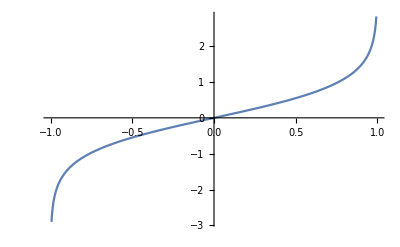

```mathematica
Plot[ArcTanh[x],{x,-1,1}]
```

```mathematica
Series[EllipticF[ArcCos[(M-a)/(M-b)],m],{M,Infinity,0}]//Simplify[#,M>0&a>0&b>0]&
```

Piecewise[{{(√(1/M))/(√(1/(2 a-2 b)))+O[1/M]^1, Arg[(b (-a+b))/(b-M)]<0}, {√2 √(a-b) √(1/M)+O[1/M]^1, True}}]

```mathematica
Series[-(√2 Hypergeometric2F1[-1/6,1/2,5/6,-(M u^3)/2])/(√(M u))/.u->1,{M,Infinity,1}]
```

-(2^(1/3) Gamma[2/3] Gamma[5/6] (1/M)^(1/3))/(√π)+(3 Gamma[5/6])/(Gamma[-1/6] M)+O[1/M]^(4/3)

```mathematica
-(2^(1/3) Gamma[2/3] Gamma[5/6] (1/M)^(1/3))/(√π)//N
```

-1.08652 (1/M)^(1/3)

```mathematica
-(2^(1/3)√Pi Gamma[5/6] (1/M)^(1/3))/Gamma[1/3]//N
```

-0.940952 (1/M)^(1/3)